# Scattering Kernels in 3D

This is code to accompany the book:
A Hitchhiker’s Guide to Multiple Scattering
© 2020 Eugene d’Eon 
www.eugenedeon.com/hitchhikers

## Isotropic Scattering

```mathematica
pIsotropic[u_]:=1/(4Pi)
```

### Normalization condition

```mathematica
Integrate[2 Pi pIsotropic[u],{u,-1,1}]
```

1

### Mean-cosine

```mathematica
Integrate[2 Pi pIsotropic[u]u,{u,-1,1}]
```

0

### Legendre expansion coefficients

```mathematica
Integrate[2 Pi (2k+1)pIsotropic[Cos[y]]LegendreP[k,Cos[y]]Sin[y]/.k->0,{y,0,Pi}]
```

1

```mathematica
Integrate[2 Pi (2k+1)pIsotropic[Cos[y]]LegendreP[k,Cos[y]]Sin[y]/.k->1,{y,0,Pi}]
```

0

### sampling

```mathematica
cdf=Integrate[2 Pi pIsotropic[u],{u,-1,x}]
```

(1+x)/2

```mathematica
Solve[cdf==e,x]
```

{{x→-1+2 e}}

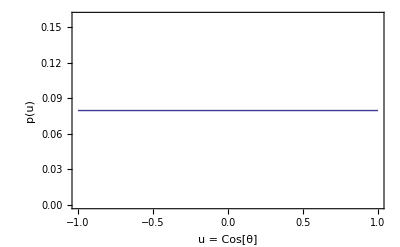

```mathematica
Clear[u];Show[
Plot[pIsotropic[u],{u,-1,1},PlotStyle->Thick]
,Frame->True,
FrameLabel->{{p[u],},{"u = Cos[θ]","Isotropic Scattering"}}]
```

## Linearly-Anisotropic Scattering (Eddington)

```mathematica
pLinaniso[u_,b_]:=1/(4 Pi)(1+b u)
```

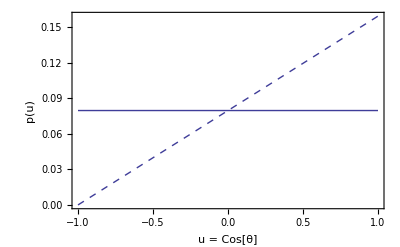

```mathematica
Clear[u];
Show[
Plot[pIsotropic[u],{u,-1,1},PlotStyle->Thick],
Plot[pLinaniso[u,1],{u,-1,1},PlotStyle->Dashed]
,Frame->True,
FrameLabel->{{p[u],},{"u = Cos[θ]","Linearly-Anisotropic Scattering"}}]
```

### Normalization condition

```mathematica
Integrate[2 Pi pLinaniso[u,b],{u,-1,1},Assumptions->b>-1&&b<1]
```

1

### Mean cosine (g)

```mathematica
Integrate[2 Pi pLinaniso[u,b]u,{u,-1,1},Assumptions->b>-1&&b<1]
```

b/3

### Legendre expansion coefficients

```mathematica
Integrate[2Pi(2k+1)pLinaniso[Cos[y],b]LegendreP[k,Cos[y]]Sin[y]/.k->0,{y,0,Pi}]
```

1

```mathematica
Integrate[2Pi(2k+1)pLinaniso[Cos[y],b]LegendreP[k,Cos[y]]Sin[y]/.k->1,{y,0,Pi}]
```

b

### sampling

```mathematica
cdf=Integrate[2 Pi pLinaniso[u,b],{u,-1,x}]
```

1/2-b/4+x/2+(b x^2)/4

```mathematica
Solve[cdf==e,x]
```

{{x→(-1-√(1-2 b+b^2+4 b e))/b},{x→(-1+√(1-2 b+b^2+4 b e))/b}}

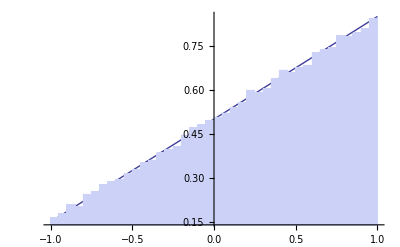

```mathematica
b=0.7;
Show[
Plot[2 Pi pLinaniso[u,b],{u,-1,1}],
Histogram[Map[(-1+√(1-2 b+b^2+4 b #))/b&,Table[RandomReal[],{i,1,100000}]],50,"PDF"]
]
Clear[b];
```

## Rayleigh Scattering

General form:

```mathematica
pRayleigh[u_,γ_]:=1/(4 Pi)3/(4(1+2γ))((1+3γ)+(1-γ)u^2)
```

Common special case (γ = 0):

```mathematica
pRayleigh[u_]:=(1+u^2)3/(16 Pi)
```

### Normalization condition

```mathematica
Integrate[2 Pi pRayleigh[u],{u,-1,1}]
```

1

```mathematica
Integrate[2 Pi pRayleigh[u,y],{u,-1,1},Assumptions->y>0]//Simplify
```

1

### Mean cosine (g)

```mathematica
Integrate[2 Pi pRayleigh[u]u,{u,-1,1}]
```

0

```mathematica
Integrate[2 Pi pRayleigh[u,y] u,{u,-1,1},Assumptions->y>0]//Simplify
```

0

### Legendre expansion coefficients

```mathematica
Integrate[2Pi(2k+1)pRayleigh[Cos[y]]LegendreP[k,Cos[y]]Sin[y]/.k->0,{y,0,Pi}]
```

1

```mathematica
Integrate[2Pi(2k+1)pRayleigh[Cos[y]]LegendreP[k,Cos[y]]Sin[y]/.k->1,{y,0,Pi}]
```

0

```mathematica
Integrate[2Pi(2k+1)pRayleigh[Cos[y]]LegendreP[k,Cos[y]]Sin[y]/.k->2,{y,0,Pi}]
```

1/2

### sampling

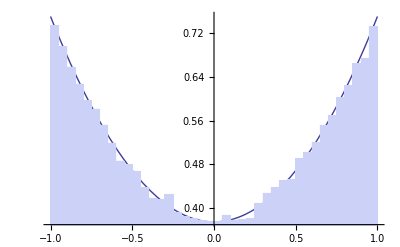

```mathematica
Show[
Plot[2 Pi pRayleigh[u],{u,-1,1}],
Histogram[Map[(1-(2-4 #+√(5+16 (-1+#)#))^(2/3))/(2-4 #+√(5+16 (-1+#) #))^(1/3)&,Table[RandomReal[],{i,1,100000}]],50,"PDF"]
]
Clear[b];
```

## Lambertian Sphere

geometrical optics far-field phase function of a white Lambertian sphere in 3D:
[Schoenberg 1929] - doi: 10.1007/978-3-642-90703-6_1
[Esposito and Lumme 1977, Blinn 1982, Porco et al. 2008]

```mathematica
pLambertSphere[u_]:=(2 (√(1-u^2)-u ArcCos[u]))/(3 π^2)
```

### MC testing

sample uniformly from a Disk in the [x,y] plane in 3D (z = 0)

```mathematica
DiskSample3D[]:=√RandomReal[]{Cos[#],Sin[#],0}&[RandomReal[] 2 Pi]
```

project down onto a 3D sphere, build a coordinate frame, and sample a white Lambertian BRDF

```mathematica
lambertspheresample[]:=Module[{p,Z,X,Y,w,s},
p=DiskSample3D[];
p[[3]]=√(1-p[[1]]^2-p[[2]]^2);
(* building basis, X,Y,Z *)
Z=p;
X=Normalize[Cross[Z,{1,0,0}]];
Y=Cross[X,Z];
(* sample Lambertian reflectance *)
w=√RandomReal[];
p=RandomReal[{0,2Pi}];
s=√(1-w^2);
(* rotate into space of selected sphere normal p *)
-(s Cos[p] X + s Sin[p] Y + w Z)
]
```

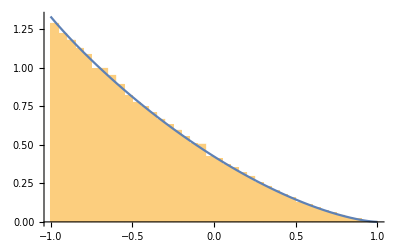

```mathematica
Show[
Histogram[Table[lambertspheresample[][[3]],{i,Range[100000]}],50,"PDF"],
Plot[2 Pi pLambertSphere[u],{u,-1,1}]
]
```

### Normalization condition

```mathematica
Integrate[2 Pi pLambertSphere[u],{u,-1,1}]
```

1

### forward scattering probability

```mathematica
Clear[u];Integrate[2 Pi pLambertSphere[u],{u,0,1}]
```

1/6

### Mean cosine (g)

```mathematica
Integrate[2 Pi pLambertSphere[u]u,{u,-1,1}]
```

-4/9

### Mean square cosine

```mathematica
Integrate[2 Pi pLambertSphere[u] u^2,{u,-1,1}]
```

3/8

This phase function is not particularly well approximated by Henyey Greenstein:

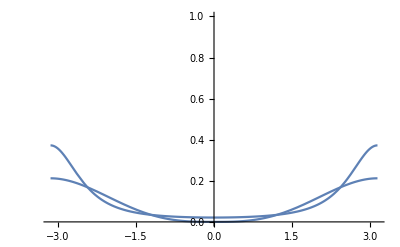

```mathematica
Show[
Plot[pHG[Cos[t],-4/9],{t,-Pi,Pi},PlotRange->{0,1}],
Plot[pLambertSphere[Cos[t]],{t,-Pi,Pi},PlotRange->All]
]
```

### Legendre expansion coefficients

```mathematica
Integrate[2Pi(2k+1)pLambertSphere[Cos[y]]LegendreP[k,Cos[y]]Sin[y]/.k->0,{y,0,Pi}]
```

1

```mathematica
Integrate[2Pi(2k+1)pLambertSphere[Cos[y]]LegendreP[k,Cos[y]]Sin[y]/.k->1,{y,0,Pi}]
```

-4/3

```mathematica
Integrate[2Pi(2k+1)pLambertSphere[Cos[y]]LegendreP[k,Cos[y]]Sin[y]/.k->2,{y,0,Pi}]
```

5/16

```mathematica
Integrate[2Pi(2k+1)pLambertSphere[Cos[y]]LegendreP[k,Cos[y]]Sin[y]/.k->3,{y,0,Pi}]
```

0

```mathematica
Integrate[2Pi(2k+1)pLambertSphere[Cos[y]]LegendreP[k,Cos[y]]Sin[y]/.k->4,{y,0,Pi}]
```

1/64

```mathematica
Integrate[2Pi(2k+1)pLambertSphere[Cos[y]]LegendreP[k,Cos[y]]Sin[y]/.k->6,{y,0,Pi}]
```

13/4096

```mathematica
Integrate[2Pi(2k+1)pLambertSphere[Cos[y]]LegendreP[k,Cos[y]]Sin[y]/.k->8,{y,0,Pi}]
```

17/16384

```mathematica
Integrate[2Pi(2k+1)pLambertSphere[Cos[y]]LegendreP[k,Cos[y]]Sin[y]/.k->10,{y,0,Pi}]
```

343/786432

### Importance sampling:

The cosine of deflection can be sampled from:

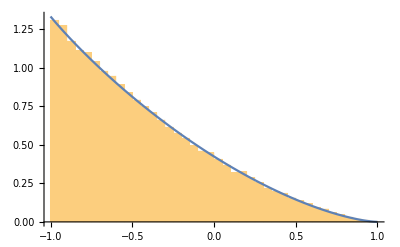

```mathematica
Show[
Histogram[Table[
Sin[2 Pi RandomReal[]] √((1-#1)(1-#2))-√(#1 #2)&[RandomReal[],RandomReal[]]
,{i,Range[100000]}],50,"PDF"],
Plot[2 Pi pLambertSphere[u],{u,-1,1}]
]
```

Approximate CDF inverse:

```mathematica
lambertSphereApproxCDFi[x_]:=1-2 (1-x^(1.01938+0.0401885 x))^0.397225
```

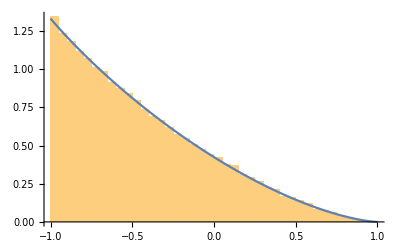

```mathematica
Show[
Histogram[Table[
lambertSphereApproxCDFi[RandomReal[]]
,{i,Range[100000]}],50,"PDF"],
Plot[2 Pi pLambertSphere[u],{u,-1,1}]
]
```

## Callisto

[Porco et al. 2008] - doi: 10.1088/0004-6256/136/5/2172

```mathematica
pCallisto[u_]:=HeavisideTheta[2.521-ArcCos[-u]] 2.2/(4 Pi (1.0004369822233856))(2-0.79333 ArcCos[-u]+Exp[-21.2 ArcCos[-u]])(1+Sin[ArcCos[-u]/2]Tan[ArcCos[-u]/2]Log[Tan[ArcCos[-u]/4]])
```

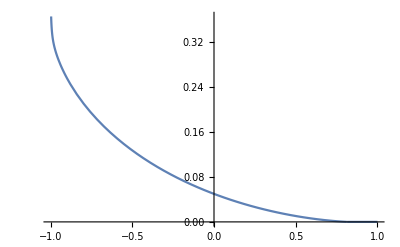

```mathematica
Plot[pCallisto[u],{u,-1,1}]
```

### Normalization condition

```mathematica
NIntegrate[ 2 Pi pCallisto[u],{u,-1,1}]
```

1.

### Mean cosine (g)

```mathematica
NIntegrate[2 Pi pCallisto[u]u,{u,-1,1}]
```

-0.560001

### Legendre expansion coefficients

```mathematica
NIntegrate[2Pi(2k+1)pCallisto[Cos[y]]LegendreP[k,Cos[y]]Sin[y]/.k->0,{y,0,Pi}]
```

1.

```mathematica
NIntegrate[2Pi(2k+1)pCallisto[Cos[y]]LegendreP[k,Cos[y]]Sin[y]/.k->1,{y,0,Pi}]
```

-1.68

```mathematica
NIntegrate[2Pi(2k+1)pCallisto[Cos[y]]LegendreP[k,Cos[y]]Sin[y]/.k->2,{y,0,Pi}]
```

0.851712

```mathematica
NIntegrate[2Pi(2k+1)pCallisto[Cos[y]]LegendreP[k,Cos[y]]Sin[y]/.k->3,{y,0,Pi}]
```

-0.285211

```mathematica
NIntegrate[2Pi(2k+1)pCallisto[Cos[y]]LegendreP[k,Cos[y]]Sin[y]/.k->4,{y,0,Pi}]
```

0.182995

```mathematica
NIntegrate[2Pi(2k+1)pCallisto[Cos[y]]LegendreP[k,Cos[y]]Sin[y]/.k->6,{y,0,Pi}]
```

0.0908047

```mathematica
NIntegrate[2Pi(2k+1)pCallisto[Cos[y]]LegendreP[k,Cos[y]]Sin[y]/.k->8,{y,0,Pi}]
```

0.064234

```mathematica
NIntegrate[2Pi(2k+1)pCallisto[Cos[y]]LegendreP[k,Cos[y]]Sin[y]/.k->10,{y,0,Pi}]
```

0.0552028

## Henyey-greenstein Scattering

[Henyey and Greestein 1940] - “Diffuse radiation in the Galaxy”

```mathematica
Clear[pHG];pHG[dot_,g_]:=1/(4 Pi)(1-g^2)/((1+g^2-2g dot)^(3/2))
```

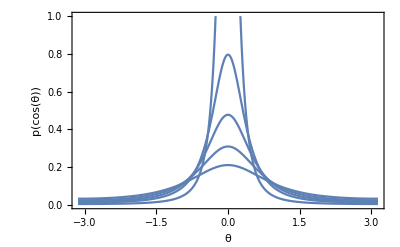

```mathematica
pHGplot=Show[
Plot[pHG[Cos[t],.8],{t,-Pi,Pi},PlotRange->{0,1}],
Plot[pHG[Cos[t],.6],{t,-Pi,Pi},PlotRange->All],
Plot[pHG[Cos[t],.5],{t,-Pi,Pi},PlotRange->All],
Plot[pHG[Cos[t],.4],{t,-Pi,Pi},PlotRange->All],
Plot[pHG[Cos[t],.3],{t,-Pi,Pi},PlotRange->All],
Frame->True,
ImageSize->400,
FrameLabel->{{p[Cos[θ]],},{θ,"Henyey-Greenstein Scattering, g = 0.3, 0.4, 0.5, 0.6, 0.8"}}]
```

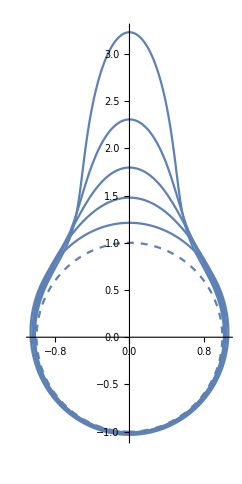

```mathematica
Show[
ParametricPlot[{Sin[t],Cos[t]}(1),{t,-Pi,Pi},PlotRange->All,PlotStyle->Dashed],
ParametricPlot[{Sin[t],Cos[t]}(1+pHG[Cos[t],0.75]),{t,-Pi,Pi},PlotRange->All],
ParametricPlot[{Sin[t],Cos[t]}(1+pHG[Cos[t],0.68]),{t,-Pi,Pi},PlotRange->All],
ParametricPlot[{Sin[t],Cos[t]}(1+pHG[Cos[t],0.6]),{t,-Pi,Pi},PlotRange->All],
ParametricPlot[{Sin[t],Cos[t]}(1+pHG[Cos[t],0.5]),{t,-Pi,Pi},PlotRange->All],
ParametricPlot[{Sin[t],Cos[t]}(1+pHG[Cos[t],0.3]),{t,-Pi,Pi},PlotRange->All]
]
```

### Normalization condition

```mathematica
Integrate[2 Pi pHG[u,g],{u,-1,1},Assumptions->g>-1&&g<1]
```

1

### Legendre expansion coefficients

```mathematica
Integrate[2Pi(2k+1)pHG[u,g]LegendreP[k,u]/.k->0,{u,-1,1},Assumptions->g>-1&&g<1]
```

1

```mathematica
Integrate[2Pi(2k+1)pHG[u,g]LegendreP[k,u]/.k->1,{u,-1,1},Assumptions->g>-1&&g<1]
```

3 g

```mathematica
Integrate[2Pi(2k+1)pHG[u,g]LegendreP[k,u]/.k->2,{u,-1,1},Assumptions->g>-1&&g<1]
```

5 g^2

```mathematica
Integrate[2Pi(2k+1)pHG[u,g]LegendreP[k,u]/.k->3,{u,-1,1},Assumptions->g>-1&&g<1]
```

7 g^3

```mathematica
Integrate[2Pi(2k+1)pHG[u,g]LegendreP[k,u]/.k->4,{u,-1,1},Assumptions->g>-1&&g<1]
```

9 g^4

### sampling

```mathematica
cdf=Integrate[2 Pi pHG[u,g],{u,-1,x},Assumptions->g>-1&&g<1&&x<1]
```

((-1+g) (-1-g+√(1+g^2-2 g x)))/(2 g √(1+g^2-2 g x))

```mathematica
Solve[cdf==e,x]
```

{{x→(-1+2 e+2 g-2 e g+2 e^2 g-g^2+2 e g^2-2 e g^3+2 e^2 g^3)/(1-g+2 e g)^2}}

```mathematica
FullSimplify[%]
```

{{x→-((-1+g)^2+2 e (-1+g) (1+g^2)-2 e^2 (g+g^3))/(1+(-1+2 e) g)^2}}

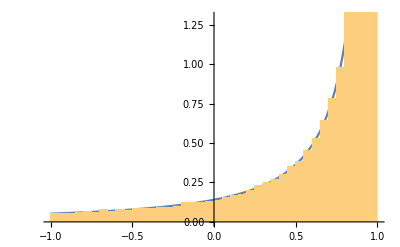

```mathematica
g=0.7;
Show[
Plot[2 Pi pHG[u,g],{u,-1,1}],
Histogram[Map[-((-1+g)^2+2 # (-1+g) (1+g^2)-2 #^2 (g+g^3))/(1+(-1+2 #) g)^2&,Table[RandomReal[],{i,1,100000}]],50,"PDF"]
]
Clear[b,g];
```

When cosine u has been sampled with random variable ξ, what is the PDF at the sampled direction in terms of ξ?

```mathematica
FullSimplify[pHG[-((-1+g)^2+2 (-1+g) (1+g^2) ξ-2 (g+g^3) ξ^2)/(1+g (-1+2 ξ))^2,g],Assumptions->-1<g<1&&0<ξ<1]
```

(1+g (-1+2 ξ))^3/(4 (-1+g^2)^2 π)

## Haltrin

[Haltrin 1988] - a phase function such that the asymptotic mode in plane geometry has an exact solution:

```mathematica
pHaltrin[u_,g_]:=1/(4 Pi)(2 g DiracDelta[1-u]+(1-g)/(√(2(1-u))))
```

### Normalization condition

```mathematica
Integrate[2 Pi pHaltrin[u,g],{u,-1,1},Assumptions->g>-1&&g<1]/.HeavisideTheta[0]->1
```

1

### Mean cosine (g)

```mathematica
Integrate[2 Pi pHaltrin[u,g]u,{u,-1,1}]/.HeavisideTheta[0]->1//FullSimplify
```

1/3 (1+2 g)

### Legendre expansion coefficients

```mathematica
Integrate[2Pi(2k+1)pHaltrin[u,g]LegendreP[k,u]/.k->0,{u,-1,1},Assumptions->g>-1&&g<1]/.HeavisideTheta[0]->1
```

1

```mathematica
Integrate[2Pi(2k+1)pHaltrin[u,g]LegendreP[k,u]/.k->1,{u,-1,1},Assumptions->g>-1&&g<1]/.HeavisideTheta[0]->1
```

1+2 g

```mathematica
Integrate[2Pi(2k+1)pHaltrin[u,g]LegendreP[k,u]/.k->2,{u,-1,1},Assumptions->g>-1&&g<1]/.HeavisideTheta[0]->1
```

1+4 g

```mathematica
Integrate[2Pi(2k+1)pHaltrin[u,g]LegendreP[k,u]/.k->3,{u,-1,1},Assumptions->g>-1&&g<1]/.HeavisideTheta[0]->1
```

1+6 g

```mathematica
Integrate[2Pi(2k+1)pHaltrin[u,g]LegendreP[k,u]/.k->4,{u,-1,1},Assumptions->g>-1&&g<1]/.HeavisideTheta[0]->1
```

1+8 g

## Kagiwada-Kalaba (Ellipsoidal) Scattering

```mathematica
pEllipsoidal[u_,b_]:=b(2 Pi Log[(1+b)/(1-b)](1-b u))^-1
```

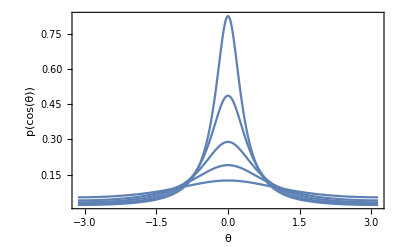

```mathematica
pEllplot=Show[
Plot[pEllipsoidal[Cos[t],.9],{t,-Pi,Pi},PlotRange->All],
Plot[pEllipsoidal[Cos[t],.8],{t,-Pi,Pi},PlotRange->All],
Plot[pEllipsoidal[Cos[t],.65],{t,-Pi,Pi},PlotRange->All],
Plot[pEllipsoidal[Cos[t],.4],{t,-Pi,Pi},PlotRange->All],
Plot[pEllipsoidal[Cos[t],.95],{t,-Pi,Pi},PlotRange->All],
Frame->True,
ImageSize->400,
FrameLabel->{{p[Cos[θ]],},{θ,"Ellipsoidal Scattering, b = 0.4, 0.65, 0.8, 0.9, 0.95"}}]
```

### sampling

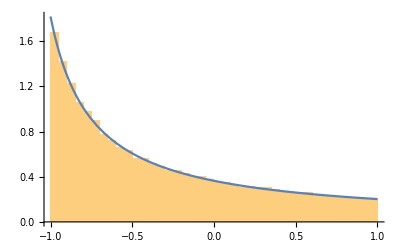

```mathematica
b=-0.8;
Show[Histogram[Map[(1-(1+b) ((1+b)/(1-b))^-#)/b&,Table[RandomReal[],{i,1,100000}]],50,"PDF"],
Plot[2 Pi pEllipsoidal[u,b],{u,-1,1}]

]
Clear[b];
```

When cosine u has been sampled with random variable ξ, what is the PDF at the sampled direction in terms of ξ?

```mathematica
FullSimplify[pEllipsoidal[(1-(1+b) ((1+b)/(1-b))^-#)/b&[ξ],b],Assumptions->0<b<1&&0<ξ<1]
```

((1-b)^-ξ b (1+b)^(-1+ξ))/(2 π Log[(1+b)/(1-b)])

### Expansion coefficients

```mathematica
Integrate[2Pi(2k+1)pEllipsoidal[u,b]LegendreP[k,u]/.k->0,{u,-1,1},Assumptions->0<b<1]/.Log[(1+b)/(1-b)]->2 ArcTanh[b]
```

1

```mathematica
Integrate[2Pi(2k+1)pEllipsoidal[u,b]LegendreP[k,u]/.k->1,{u,-1,1},Assumptions->0<b<1]/.Log[(1+b)/(1-b)]->2 ArcTanh[b]//FullSimplify
```

3/b-3/ArcTanh[b]

```mathematica
Integrate[2Pi(2k+1)pEllipsoidal[u,b]LegendreP[k,u]/.k->2,{u,-1,1},Assumptions->0<b<1]/.Log[(1+b)/(1-b)]->2 ArcTanh[b]//FullSimplify
```

5/2 (-1+3/b^2-3/(b ArcTanh[b]))

```mathematica
Integrate[2Pi(2k+1)pEllipsoidal[u,b]LegendreP[k,u]/.k->3,{u,-1,1},Assumptions->0<b<1]/.Log[(1+b)/(1-b)]->2 ArcTanh[b]//FullSimplify
```

(7 (b (-15+4 b^2)+(15-9 b^2) ArcTanh[b]))/(6 b^3 ArcTanh[b])

```mathematica
Integrate[2Pi(2k+1)pEllipsoidal[u,b]LegendreP[k,u]/.k->4,{u,-1,1},Assumptions->0<b<1]/.Log[(1+b)/(1-b)]->2 ArcTanh[b]//FullSimplify
```

(15 b (-21+11 b^2)+9 (35-30 b^2+3 b^4) ArcTanh[b])/(8 b^4 ArcTanh[b])

## Binomial Scattering

```mathematica
pBinomial[u_,n_]:=Pi^-1((n+1)/2^(n+2))(1+u)^n
```

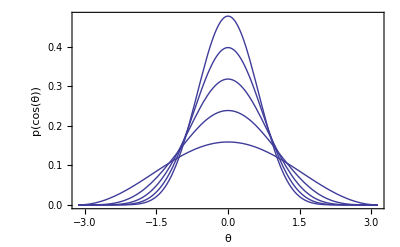

```mathematica
pBinplot=Show[
Plot[pBinomial[Cos[t],1],{t,-Pi,Pi},PlotRange->All],
Plot[pBinomial[Cos[t],2],{t,-Pi,Pi},PlotRange->All],
Plot[pBinomial[Cos[t],3],{t,-Pi,Pi},PlotRange->All],
Plot[pBinomial[Cos[t],4],{t,-Pi,Pi},PlotRange->All],
Plot[pBinomial[Cos[t],5],{t,-Pi,Pi},PlotRange->All],
Frame->True,
ImageSize->400,
FrameLabel->{{p[Cos[θ]],},{θ,"Binomial Scattering, n = 1, 2, 3, 4, 5"}}]
```

### Normalization condition

```mathematica
Integrate[2 Pi pBinomial[u,n],{u,-1,1},Assumptions->n≥0]
```

1

### Mean cosine (g)

```mathematica
Integrate[2 Pi pBinomial[u,n]u,{u,-1,1},Assumptions->n≥0]
```

n/(2+n)

### sampling

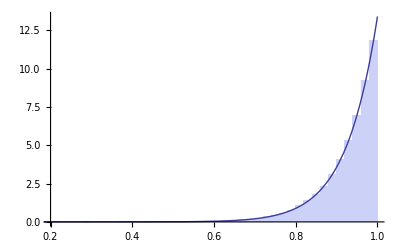

```mathematica
n=25.8;
Show[Histogram[Map[-1+(2^(1+n) #)^(1/(1+n))&,Table[RandomReal[],{i,1,100000}]],50,"PDF"],
Plot[2 Pi pBinomial[u,n],{u,-1,1},PlotRange->All]

]
Clear[b];
```

```mathematica
Integrate[2Pi(2k+1)pBinomial[u,n]LegendreP[k,u]/.k->0,{u,-1,1},Assumptions->n>1]
```

1

```mathematica
Integrate[2Pi(2k+1)pBinomial[u,n]LegendreP[k,u]/.k->1,{u,-1,1},Assumptions->n>1]
```

(3 n)/(2+n)

```mathematica
Integrate[2Pi(2k+1)pBinomial[u,n]LegendreP[k,u]/.k->2,{u,-1,1},Assumptions->n>1]
```

(5 (-1+n) n)/(6+5 n+n^2)

```mathematica
Integrate[2Pi(2k+1)pBinomial[u,n]LegendreP[k,u]/.k->3,{u,-1,1},Assumptions->n>1]
```

(7 (-2+n) (-1+n) n)/((2+n) (3+n) (4+n))

```mathematica
Integrate[2Pi(2k+1)pBinomial[u,n]LegendreP[k,u]/.k->4,{u,-1,1},Assumptions->n>1]
```

(9 (-3+n) (-2+n) (-1+n) n)/((2+n) (3+n) (4+n) (5+n))

```mathematica
Integrate[2Pi(2k+1)pBinomial[u,n]LegendreP[k,u]/.k->11,{u,-1,1},Assumptions->n>1]/(((1+2 j) Gamma[2+n])/(Gamma[1-j+n] Pochhammer[1+n,1+j])/.j->11)//FullSimplify
```

1

## Liu Scattering

```mathematica
pLiu[u_,e_,m_]:=(e(2m+1)(1+e u)^(2m))/(2 Pi((1+e)^(2m+1)-(1-e)^(2m+1)))
```

```mathematica
Clear[m]
```

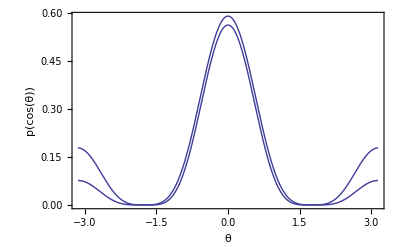

```mathematica
pLiuplot=Show[
Plot[pLiu[Cos[t],4,2],{t,-Pi,Pi},PlotRange->All],
Plot[pLiu[Cos[t],7,2],{t,-Pi,Pi},PlotRange->All],
Frame->True,
ImageSize->400,
FrameLabel->{{p[Cos[θ]],},{θ,"Liu Scattering, (m = 2, ϵ = 4), (m = 2, ϵ = 7)"}}]
```

### Normalization condition

```mathematica
Integrate[2 Pi pLiu[u,e,m],{u,-1,1},Assumptions->e>0&&m>0&&m∈Integers]
```

1

### Mean cosine (g)

```mathematica
Integrate[2 Pi u pLiu[u,e,m],{u,-1,1},Assumptions->e>0&&m>0&&m∈Integers&&e<1]
```

((1+e)^(1+2 m) (-1+e+2 e m)+(1-e)^(1+2 m) (1+e+2 e m))/(2 e (-(1-e)^(1+2 m)+(1+e)^(1+2 m)) (1+m))

### Legendre expansion coefficients

```mathematica
Integrate[2Pi(2k+1) pLiu[u,e,m]LegendreP[k,u]/.k->0,{u,-1,1},Assumptions->m>0&&m∈Integers&&e∈Reals&&e≠0&&Abs[e]<1]
```

1

```mathematica
Integrate[2Pi(2k+1) pLiu[u,e,m]LegendreP[k,u]/.k->2,{u,-1,1},Assumptions->m>0&&m∈Integers&&e∈Reals&&e≠0&&Abs[e]<1]
```

(5 ((1+e)^(1+2 m) (3+e (-3+2 m (-3+2 e (1+m))))+(1-e)^(2 m) (-1+e) (3+e (3+2 m (3+2 e (1+m))))))/(2 e^2 (-(1-e)^(1+2 m)+(1+e)^(1+2 m)) (1+m) (3+2 m))

### sampling

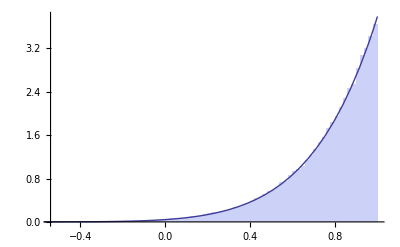

```mathematica
m=3.5;
ϵ=0.9;
Show[Histogram[Map[(-1+((-1+#) (1-ϵ)^(2 m) (-1+ϵ)+# (1+ϵ)^(1+2 m))^(1/(1+2 m)))/ϵ&,Table[RandomReal[],{i,1,100000}]],50,"PDF"],
Plot[2 Pi pLiu[u,ϵ,m],{u,-1,1},PlotRange->All]

]
Clear[m,ϵ];
```

When cosine u has been sampled with random variable ξ, what is the PDF at the sampled direction in terms of ξ?

```mathematica
FullSimplify[pLiu[(-1+((-1+#) (1-ϵ)^(2 m) (-1+ϵ)+# (1+ϵ)^(1+2 m))^(1/(1+2 m)))/ϵ&[ξ],ϵ,m],Assumptions->ϵ>0&&m>0&&0<ξ<1]
```

((1+2 m) ϵ ((1-ϵ)^(2 m) (-1+ϵ) (-1+ξ)+(1+ϵ)^(1+2 m) ξ)^((2 m)/(1+2 m)))/(2 π (-(1-ϵ)^(1+2 m)+(1+ϵ)^(1+2 m)))

## Gegenbauer Scattering

```mathematica
pGegenbauer[u_,g_,a_]:=((1 + g^2-2 g u)^(-(a+1)))/((((1-g)^(-2 a)-(1+g)^(-2 a)) π)/(a g))
```

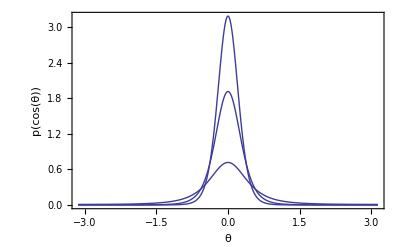

```mathematica
Show[
Plot[pGegenbauer[Cos[t],0.5,1],{t,-Pi,Pi},PlotRange->All],
Plot[pGegenbauer[Cos[t],0.5,3],{t,-Pi,Pi},PlotRange->All],
Plot[pGegenbauer[Cos[t],0.5,5],{t,-Pi,Pi},PlotRange->All],

Frame->True,
FrameLabel->{{p[Cos[θ]],},{θ,"Gegenbauer Scattering, G = 0.5, a = 1, 3, 5"}}]
```

### Normalization condition

```mathematica
Integrate[2 Pi pGegenbauer[u,g,a],{u,-1,1},Assumptions->-1≤g≤1&&a>0]
```

1

### Mean cosine (g)

```mathematica
Integrate[2 Pi u pGegenbauer[u,g,a],{u,-1,1},Assumptions->-1≤g≤1&&a>0]
```

((1+g)^(2 a) (1-2 a g+g^2)-(1-g)^(2 a) (1+2 a g+g^2))/(2 (-1+a) g ((1-g)^(2 a)-(1+g)^(2 a)))

### Legendre expansion coefficients

```mathematica
Integrate[2Pi(2k+1) pGegenbauer[u,g,a]LegendreP[k,u]/.k->0,{u,-1,1},Assumptions->-1≤g≤1&&a>0]
```

1

```mathematica
FullSimplify[Integrate[2Pi(2k+1) pGegenbauer[u,g,a]LegendreP[k,u]/.k->3,{u,-1,1},Assumptions->-1≤g≤1&&a>0]]
```

-(7 (24 a^2 g^2 (1+g^2) ((1-g)^(2 a)-(1+g)^(2 a))+3 (5+3 g^2+3 g^4+5 g^6) ((1-g)^(2 a)-(1+g)^(2 a))+8 a^3 g^3 ((1-g)^(2 a)+(1+g)^(2 a))+2 a g (15+14 g^2+15 g^4) ((1-g)^(2 a)+(1+g)^(2 a))))/(8 (-3+a) (-2+a) (-1+a) g^3 ((1-g)^(2 a)-(1+g)^(2 a)))

### sampling

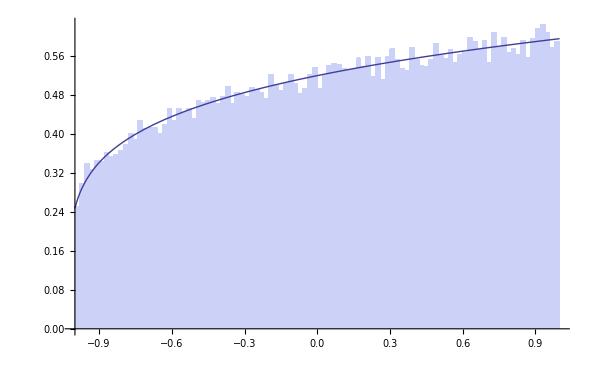

```mathematica
g=-0.8;
a=-1.2;
Show[Histogram[Map[(1+g^2-(# (1-g)^(-2 a)-(-1+#) (1+g)^(-2 a))^(-1/a))/(2 g)&,Table[RandomReal[],{i,1,100000}]],100,"PDF"],
Plot[2 Pi pGegenbauer[u,g,a],{u,-1,1},PlotRange->All]

]
Clear[g,a];
```

When cosine u has been sampled with random variable ξ, what is the PDF at the sampled direction in terms of ξ?

```mathematica
FullSimplify[pGegenbauer[(1+g^2-(# (1-g)^(-2 a)-(-1+#) (1+g)^(-2 a))^(-1/a))/(2 g)&[ξ],g,a],Assumptions->a>0&&-1<g<1&&0<ξ<1]
```

(a g ((-(1+g)^(-2 a) (-1+ξ)+(1-g)^(-2 a) ξ)^(-1/a))^(-1-a))/(((1-g)^(-2 a)-(1+g)^(-2 a)) π)

## vMF (spherical Gaussian) Scattering

[Pomraning and Prinja 1995] - “Transverse Diffusion of a Collimated Particle Beam”
https://doi.org/10.1007/BF02178551

```mathematica
pVMF[u_,k_]:=k/(4Pi  Sinh[k])Exp[k u]
```

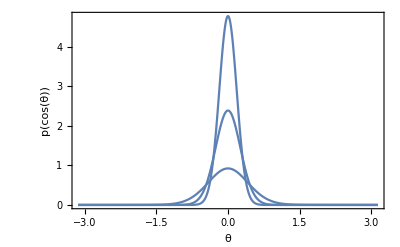

```mathematica
Show[
Plot[pVMF[Cos[t],5.8],{t,-Pi,Pi},PlotRange->All],
Plot[pVMF[Cos[t],15],{t,-Pi,Pi},PlotRange->All],
Plot[pVMF[Cos[t],30],{t,-Pi,Pi},PlotRange->All],

Frame->True,
FrameLabel->{{p[Cos[θ]],},{θ,"vMF, k = {5.8,15,30}"}}]
```

### Normalization condition

```mathematica
Integrate[2 Pi pVMF[u,k],{u,-1,1},Assumptions->k>0]
```

1

### Mean cosine (g)

```mathematica
Integrate[2 Pi u pVMF[u,k],{u,-1,1},Assumptions->k>0]
```

-1/k+Coth[k]

### Legendre expansion coefficients

```mathematica
Integrate[2Pi(2o+1)pVMF[u,k]LegendreP[o,u]/.o->0,{u,-1,1},Assumptions->k>0]
```

1

```mathematica
Integrate[2Pi(2o+1)pVMF[u,k]LegendreP[o,u]/.o->1,{u,-1,1},Assumptions->k>0]
```

-3/k+3 Coth[k]

```mathematica
Integrate[2Pi(2o+1)pVMF[u,k]LegendreP[o,u]/.o->2,{u,-1,1},Assumptions->k>0]
```

(5 (3+k^2-3 k Coth[k]))/k^2

```mathematica
Integrate[2Pi(2o+1)pVMF[u,k]LegendreP[o,u]/.o->3,{u,-1,1},Assumptions->k>0]
```

(7 (-3 (5+2 k^2)+k (15+k^2) Coth[k]))/k^3

```mathematica
Integrate[2Pi(2o+1)pVMF[u,k]LegendreP[o,u]/.o->4,{u,-1,1},Assumptions->k>0]
```

(9 (105+45 k^2+k^4-5 k (21+2 k^2) Coth[k]))/k^4

### sampling

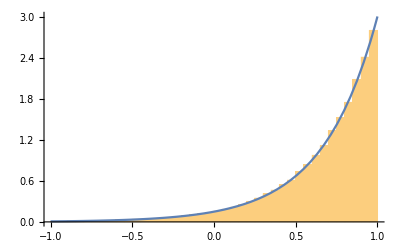

```mathematica
k=3;
Show[Histogram[Map[Log[E^-k(1-#)+E^k#]/k&,Table[RandomReal[],{i,1,100000}]],50,"PDF"],
Plot[2 Pi pVMF[u,k],{u,-1,1},PlotRange->All]

]
Clear[k];
```

When cosine u has been sampled with random variable ξ, what is the PDF at the sampled direction in terms of ξ?

```mathematica
FullSimplify[pVMF[Log[E^-k(1-#)+E^k#]/k&[ξ],k],Assumptions->k>0&&0<ξ<1]
```

(k (-1+2 ξ+Coth[k]))/(4 π)

## Klein-Nishina

Normalized variant of Klein-Nishina - energy parameter “e” = E_γ/(m_e c^2)

```mathematica
pKleinNishina[u_,e_]:=1/(1+e(1-u))1/((2 π Log[1+2 e])/e)
```

### Normalization condition

```mathematica
Integrate[2 Pi pKleinNishina[u,e],{u,-1,1},Assumptions->e>0]
```

1

### Mean-cosine

```mathematica
Integrate[2 Pi pKleinNishina[u,e]u,{u,-1,1},Assumptions->e>0]
```

1+1/e-2/Log[1+2 e]

### Legendre expansion coefficients

```mathematica
Integrate[2 Pi (2k+1)pKleinNishina[Cos[y],e]LegendreP[k,Cos[y]]Sin[y]/.k->0,{y,0,Pi},Assumptions->e>0]
```

1

```mathematica
Integrate[2 Pi (2k+1)pKleinNishina[Cos[y],e]LegendreP[k,Cos[y]]Sin[y]/.k->1,{y,0,Pi},Assumptions->e>0]
```

3+3/e-6/Log[1+2 e]

```mathematica
Integrate[2 Pi (2k+1)pKleinNishina[Cos[y],e]LegendreP[k,Cos[y]]Sin[y]/.k->2,{y,0,Pi},Assumptions->e>0]
```

5/4 (1+(3 (2+4 e+e^2-(4 e (1+e))/Log[1+2 e]))/e^2)

```mathematica
Integrate[2 Pi (2k+1)pKleinNishina[Cos[y],e]LegendreP[k,Cos[y]]Sin[y]/.k->3,{y,0,Pi},Assumptions->e>0]
```

(7 (15+45 e+36 e^2+6 e^3-(2 e (15+30 e+11 e^2))/Log[1+2 e]))/(6 e^3)

### sampling

```mathematica
cdf=Integrate[2 Pi pKleinNishina[u,e],{u,-1,x},Assumptions->e>0&&0<x<1]
```

1-Log[1+e-e x]/Log[1+2 e]

```mathematica
Solve[cdf==k,x]
```

{{x→ConditionalExpression[(1+e-(1+2 e)^(1-k))/e,-π≤Im[(-1+k) Log[1+2 e]]<π]}}

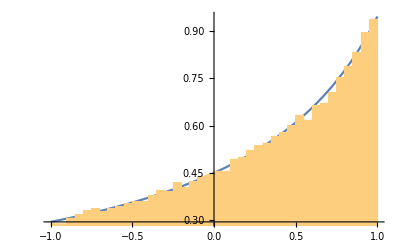

```mathematica
With[{e=1.1},

Show[
Plot[2 Pi pKleinNishina[u,e],{u,-1,1}],
Histogram[Map[(1+e-(1+2 e)^(1-#))/e&,Table[RandomReal[],{i,1,100000}]],50,"PDF"]
]
]
```

## Cornette-Shanks

[Cornette and Shanks 1992] - Physically reasonable analytic expression for the single-scattering phase function.
Independently proposed [Liu and Weng 2006]

```mathematica
pCornetteShanks[u_,g_]:=3/(8 Pi)((1-g^2)(1+u^2))/((2+g^2)(1+g^2-2 g u)^(3/2))
```

### Normalization condition

```mathematica
Integrate[2 Pi pCornetteShanks[u,g],{u,-1,1},Assumptions->-1<g<1]
```

1

### Mean-cosine

```mathematica
Integrate[2 Pi pCornetteShanks[u,g]u,{u,-1,1},Assumptions->-1<g<1]
```

(3 g (4+g^2))/(5 (2+g^2))

### Legendre expansion coefficients

```mathematica
Integrate[2 Pi (2k+1)pCornetteShanks[Cos[y],g]LegendreP[k,Cos[y]]Sin[y]/.k->0,{y,0,Pi},Assumptions->-1<g<1]
```

1

```mathematica
Integrate[2 Pi (2k+1)pCornetteShanks[Cos[y],g]LegendreP[k,Cos[y]]Sin[y]/.k->1,{y,0,Pi},Assumptions->-1<g<1]
```

(9 g (4+g^2))/(5 (2+g^2))

```mathematica
Integrate[2 Pi (2k+1)pCornetteShanks[Cos[y],g]LegendreP[k,Cos[y]]Sin[y]/.k->2,{y,0,Pi},Assumptions->-1<g<1]
```

(7+80 g^2+18 g^4)/(14+7 g^2)

```mathematica
Integrate[2 Pi (2k+1)pCornetteShanks[Cos[y],g]LegendreP[k,Cos[y]]Sin[y]/.k->3,{y,0,Pi},Assumptions->-1<g<1]
```

(g (27+238 g^2+50 g^4))/(15 (2+g^2))

### sampling

```mathematica
cdf=Integrate[2 Pi pCornetteShanks[u,g],{u,-1,x},Assumptions->-1<g<1&&0<x<1]
```

1/(4 g^3 (2+g^2) √(1+g^2-2 g x))(2-2 g^6-2 g x-2 √(1+g^2-2 g x)+4 g^3 √(1+g^2-2 g x)+g^4 (-5+x^2)+2 g^5 (x+√(1+g^2-2 g x))-g^2 (-5+x^2+4 √(1+g^2-2 g x)))

## Draine

Draine, B.T. (2003) ‘Scattering by interstellar dust grains. 1: Optical and ultraviolet’, ApJ., 598, 1017–25.

```mathematica
pDraine[u_,g_,α_]:=1/(4Pi)((1-g^2)/((1+g^2-2 g u)^(3/2))(1+α u^2)/(1+α(1+2 g^2)/3))
```

### Normalization condition

```mathematica
Integrate[2 Pi pDraine[u,g,a],{u,-1,1},Assumptions->0<a<1&&-1<g<1]
```

1

### Mean-cosine

```mathematica
Integrate[2 Pi pDraine[u,g,a]u,{u,-1,1},Assumptions->0<a<1&&-1<g<1]
```

3/5 (g+(2 (1+a) g)/(3+a+2 a g^2))

```mathematica
3/5 (g+(2 (1+a) g)/(3+a+2 a g^2))/.a->0
```

g

### Legendre expansion coefficients

```mathematica
Integrate[2 Pi (2k+1)pDraine[Cos[y],g,a]LegendreP[k,Cos[y]]Sin[y]/.k->0,{y,0,Pi},Assumptions->0<a<1&&-1<g<1]
```

1

```mathematica
Integrate[2 Pi (2k+1)pDraine[Cos[y],g,a]LegendreP[k,Cos[y]]Sin[y]/.k->1,{y,0,Pi},Assumptions->0<a<1&&-1<g<1]
```

(9 g (5+a (3+2 g^2)))/(5 (3+a+2 a g^2))

```mathematica
Integrate[2 Pi (2k+1)pDraine[Cos[y],g,a]LegendreP[k,Cos[y]]Sin[y]/.k->2,{y,0,Pi},Assumptions->0<a<1&&-1<g<1]
```

(14 a+5 (21+11 a) g^2+36 a g^4)/(7 (3+a+2 a g^2))

```mathematica
Integrate[2 Pi (2k+1)pDraine[Cos[y],g,a]LegendreP[k,Cos[y]]Sin[y]/.k->3,{y,0,Pi},Assumptions->0<a<1&&-1<g<1]
```

(g (54 a+7 (45+23 a) g^2+100 a g^4))/(15 (3+a+2 a g^2))

### sampling

```mathematica
cdf=Integrate[2 Pi pDraine[u,g,a],{u,-1,x},Assumptions->0<a<1&&-1<g<1&&-1<x<1]
```

(3 (-1+g) g^2 (-1-g+√(1+g^2-2 g x))+a (2-2 g^6-2 g x-2 √(1+g^2-2 g x)+g^3 √(1+g^2-2 g x)+g^4 (-2+x^2)+2 g^5 (x+√(1+g^2-2 g x))-g^2 (-2+x^2+√(1+g^2-2 g x))))/(2 g^3 (3+a+2 a g^2) √(1+g^2-2 g x))

## Schlick

```mathematica
pSchlick[u_,k_]:=1/(4 Pi)((1-k^2)/(1+k u)^2)
```

### Normalization condition

```mathematica
Integrate[2 Pi pSchlick[u,k],{u,-1,1},Assumptions->-1<k<1]
```

1

### Mean-cosine

```mathematica
Integrate[2 Pi pSchlick[u,k]u,{u,-1,1},Assumptions->-1<k<1]
```

-(k-ArcTanh[k]+k^2 ArcTanh[k])/k^2

### Legendre expansion coefficients

```mathematica
Integrate[2 Pi (2k+1)pSchlick[Cos[y],e]LegendreP[k,Cos[y]]Sin[y]/.k->0,{y,0,Pi},Assumptions->-1<e<1]
```

ConditionalExpression[1,e≠0]

```mathematica
Integrate[2 Pi (2k+1)pSchlick[Cos[y],e]LegendreP[k,Cos[y]]Sin[y]/.k->1,{y,0,Pi},Assumptions->-1<e<1]
```

ConditionalExpression[-(3 (e+(-1+e^2) ArcTanh[e]))/e^2,e≠0]

```mathematica
Integrate[2 Pi (2k+1)pSchlick[Cos[y],e]LegendreP[k,Cos[y]]Sin[y]/.k->2,{y,0,Pi},Assumptions->-1<e<1]
```

ConditionalExpression[-(5 (-6 e+4 e^3-6 (-1+e^2) ArcTanh[e]))/(2 e^3),e≠0]

```mathematica
Integrate[2 Pi (2k+1)pSchlick[Cos[y],e]LegendreP[k,Cos[y]]Sin[y]/.k->3,{y,0,Pi},Assumptions->-1<e<1]
```

ConditionalExpression[-(7 (30 e-26 e^3-6 (5-6 e^2+e^4) ArcTanh[e]))/(4 e^4),e≠0]

### sampling

```mathematica
cdf=Integrate[2 Pi pSchlick[u,e],{u,-1,x},Assumptions->-1<e<1&&0<x<1]
```

((1+e) (1+x))/(2+2 e x)

```mathematica
Solve[cdf==k,x]
```

{{x→(1+e-2 k)/(-1-e+2 e k)}}

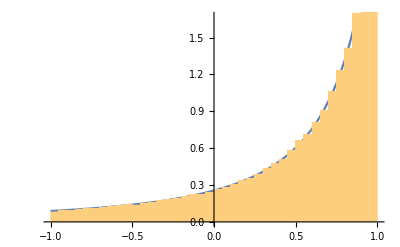

```mathematica
With[{e=-.7},
Show[
Plot[2 Pi pSchlick[u,e],{u,-1,1}],
Histogram[Map[(1+e-2 #)/(-1-e+2 e #)&,Table[RandomReal[],{i,1,100000}]],50,"PDF"]
]
]
```